## Model

### Variables

```mathematica
(*B0 to be determined with regression.*)
R =  0.02; (*Tube radius (m).*)
z0 = 0.064; (*Drop height from solenoid (m).*)
g = 9.8; (*Gravitational acceleration (m/s^2)*)
NT = 10; (*Number of wire turns.*)
Clear[B0]
```

### Models

```mathematica
AccelMotion[t_] := z0 - g t^2/2;
Field[z_] := NT B0 R^3/(R^2+z^2)^(3/2);

AccelField[t_] := Composition[Field, AccelMotion][t]
AccelVoltage[t_] := -Pi R^2 AccelField'[t]
```

### Minima

```mathematica
Clear[B0]
(*Finding minimum after time t = 0 of AccelFlux.*)
minimumVoltageModel = t/.Solve[AccelVoltage'[t] == 0, t, Reals][[3]];
(*Shifting AccelFlux minimum to t = 0.*)
AccelVoltageShifted[t_] := AccelVoltage[t + minimumVoltageModel];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

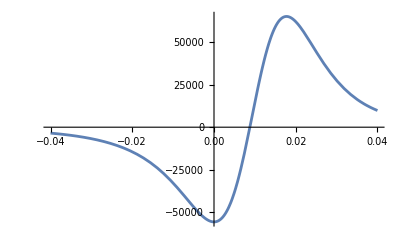

```mathematica
Clear[B0]
B0 = 100000;
Plot[AccelVoltage[t], {t, 0, 1}];
Plot[AccelVoltageShifted[t], {t, -0.04, 0.04}, PlotRange->All]
```

```mathematica
100000
```

100000

## Data

```mathematica
filePath = "C:\\Users\\Lenovo\\Documents\\Laevateinn\\School Projects\\Cuarto semestre\\Lab\\Reporte 3";
fileName = "data_test_cleaned.txt";
fullName = StringJoin[{filePath, "/", fileName}];
data = Import[fullName, "Data"];
data = data[[300;;400]];

(*We'll shift the data so as to have the first minimum at t = 0.*)
positionOfMinimum = Position[data[[All, 2]], Min[data[[All, 2]]]][[1, 1]];
timeOfMinimum = data[[positionOfMinimum, 1]];

data = MapAt[# - timeOfMinimum &, data, {All, 1}];
dataPlot = ListPlot[data]
```

Import::nffil: Importの最中にファイルC:\Users\Lenovo\Documents\Laevateinn\School Projects\Cuarto semestre\Lab\Reporte 3/data_test_cleaned.txtが見付かりませんでした．

Part::take: $Failedの300から400の位置が取れません．

Part::partd: 部分指定$Failed⟦300;;400⟧⟦All,2⟧の長さはオブジェクトの深さを超えています．

Part::partw: {}の部分1は存在しません．

Part::pkspec1: 式{{}}⟦1,1⟧は部分指定に使用できません．

MapAt::partw: $Failed⟦300;;400⟧の部分{All,1}は存在しません．

MapAt::partw: $Failed⟦300;;400⟧の部分{All,1.}は存在しません．

General::stop: この計算中に，MapAt::partwのこれ以上の出力は表示されません．

MapAt::psl: MapAt[False,False,True]の位置指定Trueは機械サイズの整数でも機械サイズの整数のリストでもありません．

MapAt::psl: MapAt[#1-1. timeOfMinimum&,$Failed⟦300;;400⟧,{All,1.}]の位置指定{All,1.}は機械サイズの整数でも機械サイズの整数のリストでもありません．

General::stop: この計算中に，MapAt::pslのこれ以上の出力は表示されません．

ListPlot::lpn: MapAt[#1-1. timeOfMinimum&,$Failed⟦300;;400⟧,{All,1.}]は数値のリストあるいは数値の対のリストではありません．

ListPlot[MapAt[#1-timeOfMinimum&,$Failed⟦300;;400⟧,{All,1}]]

## Fitting

```mathematica
Clear[B0]
fitModel = NonlinearModelFit[data, AccelVoltageShifted[t], B0, t];fitPlot = Plot[fitModel[t], {t, -0.1, 0.1}, PlotStyle->Red, PlotRange->All];

accelPlot = Plot[AccelVoltageShifted[t], {t,-0.06, 0.06}, PlotStyle->Green , PlotRange->All];

B0Fitted = B0/.fitModel["BestFitParameters"]
parameterTable = fitModel["ParameterTable"]

Show[fitPlot, dataPlot, accelPlot]
```

MapAt::partw: $Failed⟦300;;400⟧の部分{All,1.}は存在しません．

General::stop: この計算中に，MapAt::partwのこれ以上の出力は表示されません．

ReplaceAll::reps: {NonlinearModelFit[MapAt[#1-timeOfMinimum&,$Failed⟦300;;400⟧,{All,1}],-(3.88089×10^-8 B0 Cos[10 π (0.145082+t)] Sin[10 π (0.145082+t)])/((0.0004+0.004096 Cos[«1»]^2)^(5/2)),B0,t][BestFitParameters]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

B0/.NonlinearModelFit[MapAt[#1-timeOfMinimum&,$Failed⟦300;;400⟧,{All,1}],-(3.88089×10^-8 B0 Cos[10 π (0.145082+t)] Sin[10 π (0.145082+t)])/((0.0004+0.004096 Cos[10 π (0.145082+t)]^2)^(5/2)),B0,t][BestFitParameters]

NonlinearModelFit[MapAt[#1-timeOfMinimum&,$Failed⟦300;;400⟧,{All,1}],-(3.88089×10^-8 B0 Cos[10 π (0.145082+t)] Sin[10 π (0.145082+t)])/((0.0004+0.004096 Cos[10 π (0.145082+t)]^2)^(5/2)),B0,t][ParameterTable]

Show::gcomb: Show[,ListPlot[MapAt[#1-timeOfMinimum&,$Failed⟦300;;400⟧,{All,1}]],]のグラフィックスオブジェクトを組み合せることができませんでした．

Show[-Graphics-,ListPlot[MapAt[#1-timeOfMinimum&,$Failed⟦300;;400⟧,{All,1}]],-Graphics-]